## Constants

```mathematica
Get["constants.m"]
```

## QM

### Diagonalizing

```mathematica
Jx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Jy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Jz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
p={1,0,0};
```

```mathematica
p.Jx.Jx.p-(p.Jx.p)^2
```

1/2

```mathematica
SxBasis=Table[Normalize[Eigenvectors[Jx][[n]]],{n,1,3}];
```

```mathematica
JxS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jx,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
JyS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jy,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];JzS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jz,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
```

```mathematica
(*HQM=Sum[U/2 JzS[[n]].JzS[[n]]-μ JzS[[n]],{n,1,Sites}]- J navg Sum[Sum[JxS[[n]].JxS[[m]]+JyS[[n]].JyS[[m]],{m,n+1,Sites}],{n,1,Sites}];*)
```

```mathematica
ProgressIndicator[Dynamic[l],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[n],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[m],{1,Sites}]
```

```mathematica
Timing[HQM=Sum[Uvalue/2 JzS[[l]].JzS[[l]]-μvalue JzS[[l]],{l,1,Sites}]- Jvalue navgvalue Sum[Sum[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jx+Jy,IdentityMatrix[3^(m-n-1)],Jx+Jy,IdentityMatrix[3^(Sites-m)]],{{1,3,5,7,9},{2,4,6,8,10}}],{m,n+1,Sites}],{n,1,Sites}];]
```

{26.93137,Null}

```mathematica
(*Timing[{En,ψn}=Eigensystem[HQM];]*)
```

```mathematica
Timing[{En,ψn}=Eigensystem[HQM];]
```

{3.64246,Null}

```mathematica
cn=Array[c,3^Sites];
```

```mathematica
Ψ=Sum[cn[[n]] ψn[[n]] ⅇ^(-ⅈ En[[n]] t),{n,1,3^Sites}];
```

### Initial conditons

```mathematica
AvgSx[n_,time_]:=Ψ*.JxS[[n]].Ψ/.t->time;
AvgSy[n_,time_]:=Ψ*.JyS[[n]].Ψ/.t->time;
AvgSz[n_,time_]:=Ψ*.JzS[[n]].Ψ/.t->time;
```

```mathematica
cn2[f_,s_]:=Abs[Flatten[UnitVector[3,f+2]⊗UnitVector[3,s+2]].Ψ]^2;
```

```mathematica
szpp=Solve[Flatten[{1,0,0}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
szpm=Solve[Flatten[{1,0,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
szpmp=Solve[Flatten[{1,0,0}⊗{0,0,1}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,27}],cn];
```

```mathematica
szp0m=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,27}],cn];
```

```mathematica
szp0mp=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,81}],cn];
```

```mathematica
szp0mp0=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,3^Sites}],cn];
```

```mathematica
szdw=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}⊗{0,1,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,3^Sites}],cn];
```

```mathematica
szp0=Solve[Flatten[{1,0,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
sz00=Solve[Flatten[{0,1,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
sx11=Solve[Flatten[SxBasis[[2]]⊗SxBasis[[2]]]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

### Plotting

```mathematica
Timing[stufftp=AvgSz[1,t]/.szdw[[1]];]
```

{329.21852,Null}

```mathematica
Timing[Ψv=Ψ/.szdw[[1]];]
```

$Aborted

```mathematica
Timing[stufftoplot=Ψv*.JzS[[1]].Ψv;]
```

{1.80228,Null}

```mathematica
Timing[stufftoplot=Ψv*.JxS[[2]].Ψv;]
```

{2.47262,Null}

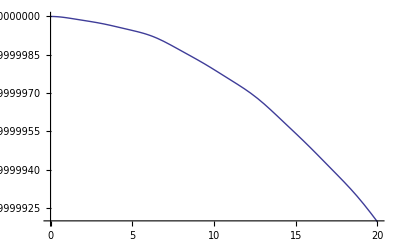
{78.8143,-Graphics-}

```mathematica
Timing[Plot[stufftoplot/.t->time,{time,0,tmax},PlotRange->All]]
```

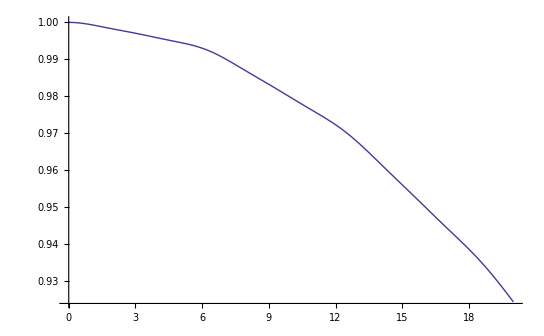
{90.36709,-Graphics-}

```mathematica
Timing[szpuj100s6=Plot[stufftp,{t,0,tmax},PlotRange->All]]
```

```mathematica
Timing[szmuj100s6=Plot[AvgSz[2,t]/.szdw[[1]],{t,0,tmax},PlotRange->All,PerformanceGoal->"Speed"]]
```

$Aborted

```mathematica
Timing[Plot[Ψv*.JzS[[1]].Ψv,{t,0,tmax},PlotRange->All]]
```

{29.50123,-Graphics-}